```mathematica
Assuming[Z>0,Integrate[r1^2r2^2(-Z r1/a0 + 2)^2(-Z r2/a0 + 2)^2 (1/(r1-r2))  Exp[-Z(r1+r2)/a0],{r1,0,Infinity},{r2,0,Infinity}]]
```

ConditionalExpression[(64 a0^6)/Z^6, Re[a0]>0]

```mathematica
Integrate[1/Abs[r1-r2] Exp[-2Z (r1+r2)/a0],{r1,0,Infinity},{r2,0,Infinity}]
```

Integrate::idiv: Integral of ⅇ^(-(2 (r1+r2) Z)/a0)/Abs[r1-r2] does not converge on {0,∞}.

∫_0^∞ ∫_0^∞ ⅇ^(-(2 (r1+r2) Z)/a0)/Abs[r1-r2]ⅆr2ⅆr1

```mathematica
Integrate[r1^2 (-Z r1/a0 + 2)^2 Exp[-Z r1/a0],{r1,0,r2}]
```

(8 a0^4-ⅇ^(-(r2 Z)/a0) (8 a0^4+8 a0^3 r2 Z+4 a0^2 r2^2 Z^2+r2^4 Z^4))/(a0 Z^3)

```mathematica
(8 a0^4-ⅇ^(-(r2 Z)/a0) (8 a0^4+8 a0^3 r2 Z+4 a0^2 r2^2 Z^2+r2^4 Z^4))/(a0 Z^3)/.{r2->Subscript[r, 2],a0->Subscript[a, 0]}//TeXForm//CopyToClipboard
```

```mathematica
Integrate[r1(-Z r1/a0 + 2)^2 Exp[-Z r1/a0],{r1,r2,Infinity}]
```

ConditionalExpression[(ⅇ^(-(r2 Z)/a0) (2 a0^3+2 a0^2 r2 Z-a0 r2^2 Z^2+r2^3 Z^3))/(a0 Z^2), Re[Z/a0]>0]

```mathematica
(ⅇ^(-(r2 Z)/a0) (2 a0^3+2 a0^2 r2 Z-a0 r2^2 Z^2+r2^3 Z^3))/(a0 Z^2)/.{r2->Subscript[r, 2],a0->Subscript[a, 0]}//TeXForm//CopyToClipboard
```

```mathematica
(8 a0^4-ⅇ^(-(r2 Z)/a0) (8 a0^4+8 a0^3 r2 Z+4 a0^2 r2^2 Z^2+r2^4 Z^4))/(r2 a0 Z^3)+(ⅇ^(-(r2 Z)/a0) (2 a0^3+2 a0^2 r2 Z-a0 r2^2 Z^2+r2^3 Z^3))/(a0 Z^2)//Together
```

(ⅇ^(-(r2 Z)/a0) (-8 a0^3+8 a0^3 ⅇ^((r2 Z)/a0)-6 a0^2 r2 Z-2 a0 r2^2 Z^2-r2^3 Z^3))/(r2 Z^3)

```mathematica
(ⅇ^(-(r2 Z)/a0) (-8 a0^3+8 a0^3 ⅇ^((r2 Z)/a0)-6 a0^2 r2 Z-2 a0 r2^2 Z^2-r2^3 Z^3))/(r2 Z^3)/.{r2->Subscript[r, 2],a0->Subscript[a, 0]}//TeXForm//CopyToClipboard
```

```mathematica
r2(ⅇ^(-(r2 Z)/a0) (-8 a0^3+8 a0^3 ⅇ^((r2 Z)/a0)-6 a0^2 r2 Z-2 a0 r2^2 Z^2-r2^3 Z^3))/Z^3(-Z r2/a0 + 2)^2 Exp[-Z r2/a0]//Expand
```

-2 ⅇ^(-(2 r2 Z)/a0) r2^4-(32 a0^3 ⅇ^(-(2 r2 Z)/a0) r2)/Z^3+(32 a0^3 ⅇ^(-(r2 Z)/a0) r2)/Z^3+(8 a0^2 ⅇ^(-(2 r2 Z)/a0) r2^2)/Z^2-(32 a0^2 ⅇ^(-(r2 Z)/a0) r2^2)/Z^2+(8 a0 ⅇ^(-(2 r2 Z)/a0) r2^3)/Z+(8 a0 ⅇ^(-(r2 Z)/a0) r2^3)/Z+(2 ⅇ^(-(2 r2 Z)/a0) r2^5 Z)/a0-(ⅇ^(-(2 r2 Z)/a0) r2^6 Z^2)/a0^2

```mathematica
exp=-2 ⅇ^(-(2 r2 Z)/a0) r2^4-(32 a0^3 ⅇ^(-(2 r2 Z)/a0) r2)/Z^3+(32 a0^3 ⅇ^(-(r2 Z)/a0) r2)/Z^3+(8 a0^2 ⅇ^(-(2 r2 Z)/a0) r2^2)/Z^2-(32 a0^2 ⅇ^(-(r2 Z)/a0) r2^2)/Z^2+(8 a0 ⅇ^(-(2 r2 Z)/a0) r2^3)/Z+(8 a0 ⅇ^(-(r2 Z)/a0) r2^3)/Z+(2 ⅇ^(-(2 r2 Z)/a0) r2^5 Z)/a0-(ⅇ^(-(2 r2 Z)/a0) r2^6 Z^2)/a0^2;
```

```mathematica
terms={-2 ⅇ^(-(2 r2 Z)/a0) r2^4,-(32 a0^3 ⅇ^(-(2 r2 Z)/a0) r2)/Z^3,(32 a0^3 ⅇ^(-(r2 Z)/a0) r2)/Z^3,(8 a0^2 ⅇ^(-(2 r2 Z)/a0) r2^2)/Z^2,-(32 a0^2 ⅇ^(-(r2 Z)/a0) r2^2)/Z^2,(8 a0 ⅇ^(-(2 r2 Z)/a0) r2^3)/Z,(8 a0 ⅇ^(-(r2 Z)/a0) r2^3)/Z,(2 ⅇ^(-(2 r2 Z)/a0) r2^5 Z)/a0,-(ⅇ^(-(2 r2 Z)/a0) r2^6 Z^2)/a0^2}
```

{-2 ⅇ^(-(2 r2 Z)/a0) r2^4,-(32 a0^3 ⅇ^(-(2 r2 Z)/a0) r2)/Z^3,(32 a0^3 ⅇ^(-(r2 Z)/a0) r2)/Z^3,(8 a0^2 ⅇ^(-(2 r2 Z)/a0) r2^2)/Z^2,-(32 a0^2 ⅇ^(-(r2 Z)/a0) r2^2)/Z^2,(8 a0 ⅇ^(-(2 r2 Z)/a0) r2^3)/Z,(8 a0 ⅇ^(-(r2 Z)/a0) r2^3)/Z,(2 ⅇ^(-(2 r2 Z)/a0) r2^5 Z)/a0,-(ⅇ^(-(2 r2 Z)/a0) r2^6 Z^2)/a0^2}

```mathematica
int=Assuming[Z>0&&a0>0,Integrate[#,{r2,0,Infinity}]]&/@terms
```

{-(3 a0^5)/(2 Z^5),-(8 a0^5)/Z^5,(32 a0^5)/Z^5,(2 a0^5)/Z^5,-(64 a0^5)/Z^5,(3 a0^5)/Z^5,(48 a0^5)/Z^5,(15 a0^5)/(4 Z^5),-(45 a0^5)/(8 Z^5)}

```mathematica
Total[int]
```

(77 a0^5)/(8 Z^5)

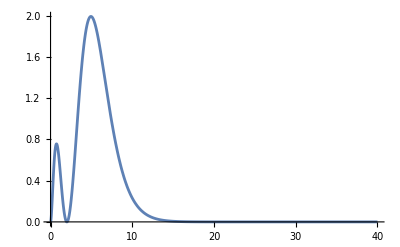

```mathematica
Plot[-1/(a0^2 Z^3)ⅇ^(-(2 r2 Z)/a0) r2 (-2 a0+r2 Z)^2 (-8 a0^3 (-1+ⅇ^((r2 Z)/a0))+6 a0^2 r2 Z+2 a0 r2^2 Z^2+r2^3 Z^3)/.{a0->1,Z->1},{r2,0,40},PlotRange->All]
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
ℏ=PlanckConstantReduced
m=ElectronMass
e=ElectronCharge
Z=2
c=SpeedOfLight
α=FineStructureConstant
ϵ0=VacuumPermittivity
```

1.05457×10^-34 Joule Second

9.10938×10^-31 Kilogram

1.60218×10^-19 Coulomb

2

(299792458 Meter)/Second

0.00729735

(625000 Ampere Second)/(22468879468420441 Meter π Volt)

```mathematica
ϵ0//N
```

(8.85419×10^-12 Ampere Second)/(Meter Volt)

```mathematica
a0=ℏ/(m c α)
```

(5.29177×10^-11 Joule Second^2)/(Kilogram Meter)

```mathematica
-m e^4/(2ℏ^2)+77/8 (4π e^2/ϵ0) Z/((32π)^2 a0)//N
```

-(2.69866×10^-38 Coulomb^4 Kilogram)/(Joule^2 Second^2)+(1.31133×10^-18 Coulomb^2 Kilogram Meter^2 Volt)/(Ampere Joule Second^3)

```mathematica
-2.698660021599987*^-38 + 1.3113292323423267*^-18
```

1.31133×10^-18

```mathematica
1.3113292323423267*^-18/(1.6*10^(-19))
```

8.19581